## Assume that particles interact with one another via a force that is repulsive at short distances and attractive at long ones

### Force

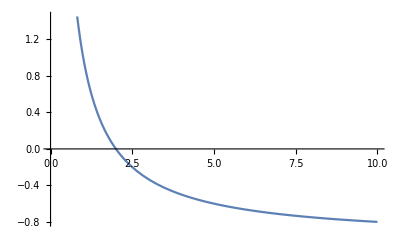

```mathematica
λ=2;
Plot[λ/x-1,{x,0,10}]
```

### Potential

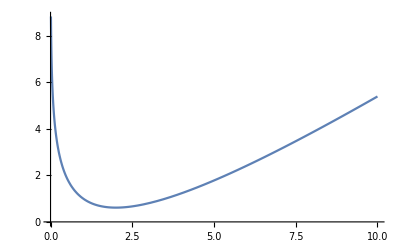

```mathematica
Plot[x-λ Log[x],{x,0,10}]
```

```mathematica
fDerivative[f_,z_]:=Module[{x,v},v=Array[x,Length[z]];
D[f@@v,{v}]/.Thread[v->z]]
fLeapFrogStep[θ_,m_,ϵ_,logP_]:=Module[{grad,x,θ1,m1,grad1},grad=fDerivative[logP,θ];m1=m+0.5 ϵ grad; θ1=θ+ϵ m1;grad1=fDerivative[logP,θ1];m1=m1+0.5 ϵ grad1;{θ1,m1}]
```

```mathematica
fForce[r_,λ_]:=1-λ/r
fForceVector[pos1__,pos2__,λ_]:=Module[{r=EuclideanDistance[pos1,pos2],rvec=pos2-pos1},(rvec / r)fForce[r,λ]]
```

```mathematica
fLeapFrogStepForce[pos1__,pos2__,p1__,λ_,ϵ_]:=Module[{f1=fForceVector[pos1,pos2,λ],p1new,pos1new},p1new=p1 + 0.5 ϵ f1;pos1new=pos1 + ϵ p1new;f1=fForceVector[pos1new,pos2,λ];
p1new=p1new + 0.5 ϵ f1;{pos1new,p1new}]
```

```mathematica
fLeapFrogStepForceBoth[pos1__,pos2__,p1__,p2__,λ_,ϵ_]:=Module[{temp=fLeapFrogStepForce[pos1,pos2,p1,λ,ϵ],pos1new,p1new},pos1new=temp[[1]];p1new=temp[[2]];
temp=fLeapFrogStepForce[pos2,pos1new,p2,λ,ϵ];{pos1new,temp[[1]],p1new,temp[[2]]}]
```

```mathematica
data=NestList[fLeapFrogStepForceBoth[#[[1]],#[[2]],#[[3]],#[[4]],1,0.1]&,{{1,3},{2,5},{0.5,0.5},{0,-0.5}},1000];
```

```mathematica
gList=Table[ListLinePlot[{data[[1;;i,1]],data[[1;;i,2]]}],{i,1,200,1}];
```

```mathematica
ListAnimate[gList]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Export["repulsion.gif",gList]
```

repulsion.gif

## Use this for an applied example

```mathematica
fLeapFrogStepForcePotential[pos1__,pos2__,p1__,λ_,ϵ_,logP_]:=Module[{f1=fForceVector[pos1,pos2,λ],p1new,pos1new,grad},grad=fDerivative[logP,pos1];p1new=p1 + 0.5 ϵ (f1+grad);pos1new=pos1 + ϵ p1new;f1=fForceVector[pos1new,pos2,λ];
grad=fDerivative[logP,pos1new];
p1new=p1new + 0.5 ϵ (f1+grad);{pos1new,p1new}]
fLeapFrogStepForcePotentialBoth[pos1__,pos2__,p1__,p2__,λ_,ϵ_,logP_]:=Module[{temp=fLeapFrogStepForcePotential[pos1,pos2,p1,λ,ϵ,logP],pos1new,p1new},pos1new=temp[[1]];p1new=temp[[2]];
temp=fLeapFrogStepForcePotential[pos2,pos1new,p2,λ,ϵ,logP];{pos1new,temp[[1]],p1new,temp[[2]]}]
```

```mathematica
logP[x__]:=Log[PDF[MultinormalDistribution[{5,5},{{1.5,1.25},{1.25,1.5}}],{x}]][[1]]
```

```mathematica
data=NestList[fLeapFrogStepForcePotentialBoth[#[[1]],#[[2]],#[[3]],#[[4]],1,0.1,logP]&,{{1,3},{2,5},{0.5,0.5},{0,-0.5}},200];
```

```mathematica
gMain=ContourPlot[Exp[logP[{x,y}]],{x,3,7},{y,3,7},ContourStyle->Black,Contours->10,ContourShading->None,PlotRange->Full];
```

```mathematica
gList=Table[Show[gMain,ListLinePlot[{data[[1;;i,1]],data[[1;;i,2]]}]],{i,1,200,1}];
```

```mathematica
ListAnimate[gList]
```

## Try for multimodal example

```mathematica
logP[x__]:=Log[PDF[MultinormalDistribution[{5,5},{{1.5,0.5},{0.5,1.5}}],{x}]+PDF[MultinormalDistribution[{15,15},{{1.5,-0.5},{-0.5,1.5}}],{x}]][[1]]
```

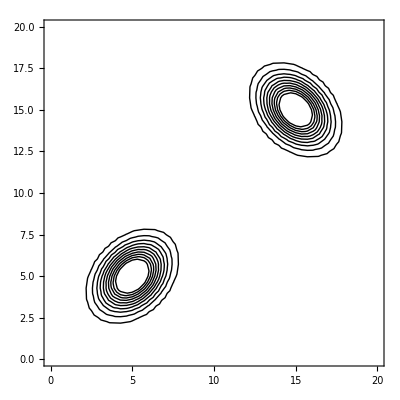

```mathematica
gMain=ContourPlot[Exp[logP[{x,y}]],{x,0,20},{y,0,20},ContourStyle->Black,Contours->10,ContourShading->None,PlotRange->Full]
```

```mathematica
data=NestList[fLeapFrogStepForcePotentialBoth[#[[1]],#[[2]],#[[3]],#[[4]],15,0.1,logP]&,{{1,3},{2,5},{0,0},{0,-0.0}},500];
```

```mathematica
gList=Table[Show[gMain,ListLinePlot[{data[[1;;i,1]],data[[1;;i,2]]}]],{i,1,500,2}];
```

```mathematica
ListAnimate[gList]
```

## Allow force to vary

```mathematica
fForce1[r_,λ_,a_]:=If[a(1-λ/r)>0,0,a(1-λ/r)]
fForceVector1[pos1__,pos2__,λ_,a_]:=Module[{r=EuclideanDistance[pos1,pos2],rvec=pos2-pos1},(rvec / r)fForce1[r,λ,a]]
```

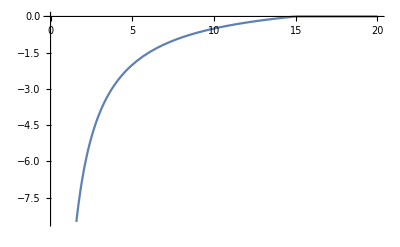

```mathematica
Plot[fForce1[r,15,1],{r,0,20}]
```

```mathematica
fLeapFrogStepForcePotential1[pos1__,pos2__,p1__,λ_,a_,ϵ_,logP_]:=Module[{f1=fForceVector1[pos1,pos2,λ,a],p1new,pos1new,grad},grad=fDerivative[logP,pos1];p1new=p1 + 0.5 ϵ (f1+grad);pos1new=pos1 + ϵ p1new;f1=fForceVector1[pos1new,pos2,λ,a];
grad=fDerivative[logP,pos1new];
p1new=p1new + 0.5 ϵ (f1+grad);{pos1new,p1new}]
fLeapFrogStepForcePotentialBoth1[pos1__,pos2__,p1__,p2__,λ_,a_,ϵ_,logP_]:=Module[{temp=fLeapFrogStepForcePotential1[pos1,pos2,p1,λ,a,ϵ,logP],pos1new,p1new},pos1new=temp[[1]];p1new=temp[[2]];
temp=fLeapFrogStepForcePotential1[pos2,pos1new,p2,λ,a,ϵ,logP];{pos1new,temp[[1]],p1new,temp[[2]]}]
```

```mathematica
data=NestList[fLeapFrogStepForcePotentialBoth1[#[[1]],#[[2]],#[[3]],#[[4]],5,0.01,0.1,logP]&,{{15,10},{2,5},{0.0,0.0},{0,-0.0}},5000];
```

```mathematica
gList=Table[Show[gMain,ListLinePlot[{data[[1;;i,1]],data[[1;;i,2]]}]],{i,1,5000,20}];
```

```mathematica
ListAnimate[gList]
```

```mathematica
Export["repulsion.gif",gList]
```

repulsion.gif

## Accelerated molecular dynamics

```mathematica
logP[x__]:=Log[PDF[MultinormalDistribution[{5,5},{{0.1,0.0},{0.0,0.1}}],{x}]+PDF[MultinormalDistribution[{15,15},{{0.2,0},{0,0.2}}],{x}]][[1]]
```

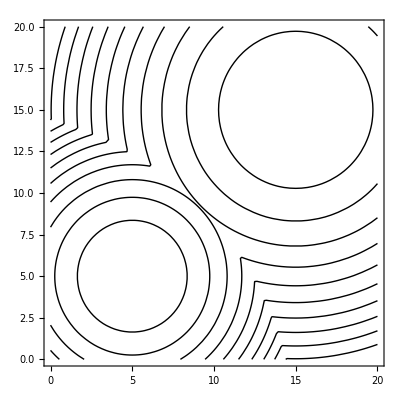

```mathematica
gMain=ContourPlot[logP[{x,y}],{x,0,20},{y,0,20},ContourStyle->Black,Contours->10,ContourShading->None,PlotRange->Full]
```

```mathematica
Plot3D[-logP[{x,y}],{x,0,20},{y,0,20},PlotRange->Full]
```

-Graphics3D-

```mathematica
fModifiedLogP[logP_,x__,E_,α_]:=If[-logP[x]>E,-logP[x],-logP[x]+(E+logP[x])^2/(α + (E+logP[x]))]
```

```mathematica
Plot3D[fModifiedLogP[logP,{x,y},200,100],{x,0,20},{y,0,20},PlotRange->Full]
```

-Graphics3D-

```mathematica
fModifiedLogP1[x__]:=Module[{logP=-fModifiedLogP[logP,x,200,10]},logP]
```

```mathematica
fDerivative[fModifiedLogP1,{1,1}]
```

Part::partd: Part specification (-159.535)⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{2.07378×10^-68+(2.07378×10^-68 (200+(-159.535)⟦1⟧)^2)/(210+(-159.535)⟦1⟧)^2-(4.14756×10^-68 (200+(-159.535)⟦1⟧))/(210+(-159.535)⟦1⟧),2.07378×10^-68+(2.07378×10^-68 (200+(-159.535)⟦1⟧)^2)/(210+(-159.535)⟦1⟧)^2-(4.14756×10^-68 (200+(-159.535)⟦1⟧))/(210+(-159.535)⟦1⟧)}

```mathematica
fDerivative[logP,{1,1}]
```

{2.07378×10^-68,2.07378×10^-68}

```mathematica
fModifiedLogP[logP,{1,1},200,100]
```

171.192

```mathematica
logP[{1,1}]
```

-159.535

```mathematica
logP1[x__]:=Module[{density=Log[PDF[MultinormalDistribution[{5,5},{{0.1,0.0},{0.0,0.1}}],{x}]+PDF[MultinormalDistribution[{15,15},{{0.2,0},{0,0.2}}],{x}]][[1]]},If[density<-200,logP[x],logP[x]-(logP[x]+200)^2/(10+(logP[x]+200))]]
```

```mathematica
Plot3D[-logP1[{x,y}],{x,0,20},{y,0,20}]
```

-Graphics3D-

```mathematica
D[logP1[{x,y}],y]
```

If[Log[0.795775 ⅇ^(1/2 (-(0.+5. (-15+x)) (-15+x)-(0.+5. (-15+y)) (-15+y)))+1.59155 ⅇ^(1/2 (-(0.+10. (-5+x)) (-5+x)-(0.+10. (-5+y)) (-5+y)))]<-200,logP^({0,1})[{x,y}],logP^({0,1})[{x,y}]+((logP[{x,y}]+200)^2 logP^({0,1})[{x,y}])/(10+(logP[{x,y}]+200))^2-(2 (logP[{x,y}]+200) logP^({0,1})[{x,y}])/(10+(logP[{x,y}]+200))]

```mathematica
dX[x_,y_]:=If[Log[0.7957747154594768 ⅇ^(1/2 (-(0.+5. (-15+x)) (-15+x)-(0.+5. (-15+y)) (-15+y)))+1.5915494309189535 ⅇ^(1/2 (-(0.+10. (-5+x)) (-5+x)-(0.+10. (-5+y)) (-5+y)))]<-200,Derivative[{1,0}][logP][{x,y}],Derivative[{1,0}][logP][{x,y}]+((logP[{x,y}]+200)^2 Derivative[{1,0}][logP][{x,y}])/(10+(logP[{x,y}]+200))^2-(2 (logP[{x,y}]+200) Derivative[{1,0}][logP][{x,y}])/(10+(logP[{x,y}]+200))]
```

```mathematica
dY[x_,y_]:=If[Log[0.7957747154594768 ⅇ^(1/2 (-(0.+5. (-15+x)) (-15+x)-(0.+5. (-15+y)) (-15+y)))+1.5915494309189535 ⅇ^(1/2 (-(0.+10. (-5+x)) (-5+x)-(0.+10. (-5+y)) (-5+y)))]<-200,Derivative[{0,1}][logP][{x,y}],Derivative[{0,1}][logP][{x,y}]+((logP[{x,y}]+200)^2 Derivative[{0,1}][logP][{x,y}])/(10+(logP[{x,y}]+200))^2-(2 (logP[{x,y}]+200) Derivative[{0,1}][logP][{x,y}])/(10+(logP[{x,y}]+200))]
```

```mathematica
fDerivative[x_,y_]:={dX[x,y],dY[x,y]}
```

```mathematica
fLeapFrogStep[θ_,m_,ϵ_]:=Module[{grad,x,θ1,m1,grad1},grad=fDerivative[θ[[1]],θ[[2]]];m1=m+0.5 ϵ grad; θ1=θ+ϵ m1;grad1=fDerivative[θ1[[1]], θ1[[2]]];m1=m1+0.5 ϵ grad1;{θ1,m1}]
fLeapFrogSteps[θ_,m_,ϵ_,L_Integer]:=NestList[fLeapFrogStep[#[[1]],#[[2]],ϵ]&,{θ,m},L][[-1]]
```

```mathematica
fHMCStep[θ_,ϵ_,L_Integer]:=Module[{m=RandomVariate[NormalDistribution[0,1],2],theta,m1,r=RandomReal[],res},res=fLeapFrogSteps[θ,m,ϵ,L];
theta=res[[1]];m1=res[[2]];
If[Exp[logP1[θ]-logP1[theta]+PDF[MultinormalDistribution[{0,0},IdentityMatrix[2]],m1]-PDF[MultinormalDistribution[{0,0},IdentityMatrix[2]],m]]>r,theta,θ]]
fHMC[n_Integer,θ0_,ϵ_,L_Integer]:=NestList[fHMCStep[#,ϵ,L]&,θ0,n]
```

```mathematica
ldata=fHMC[100,{1,1},0.1,10];
```

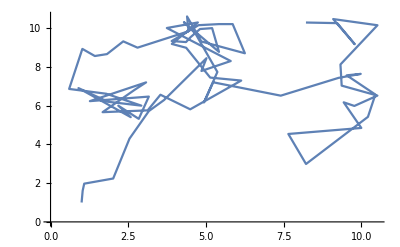

```mathematica
ListLinePlot[ldata]
```

```mathematica
deltaV[θ_]:=logP[θ]-logP1[θ]
```

```mathematica
-deltaV/@ldata
```

{-11.657,-48.1169,-50.4814,-0.36731,-39.1079,-57.6895,-1.87548,-94.6478,-115.709,-125.156,-126.687,-131.435,-130.852,-125.418,-120.49,-102.081,-66.5277,-62.0803,-97.3356,-107.353,-102.142,-14.2993,-12.5312,-74.9295,-43.5153,-52.4944,-58.0193,-87.7231,-99.075,-127.079,-118.592,-121.353,-121.695,-99.1777,-77.687,-98.6011,-92.1054,-54.5408,-45.9842,-91.7903,-69.162,-90.8371,-96.7741,-73.4369,-43.4931,-36.5576,-86.7683,-98.6424,-113.248,-104.142,-89.3468,-109.043,-112.603,-79.8852,-0.0214888,-0.0214888,-69.7433,-55.3111,-22.938,-21.8453,-55.9614,-95.3002,-105.443,-83.7599,-99.6879,-109.646,-66.3274,-39.1572,-52.4463,-60.3056,-32.2851,-4.07331,-15.4422,-0.0851056,-47.1094,-91.2879,-50.2827,-45.0195,-69.4885,-67.4292,-58.8394,-63.3083,-48.8828,-50.235,-59.2884,-72.6378,-84.2194,-88.1759,-76.6483,-22.57,-27.3175,-15.7331,0.,0.,0.,0.,0.,0.,0.,-55.3312,-24.9981}

## Eggbox